```mathematica
(***************
This is the 3rd version of script of Enqvist model for A-B nucleation.

The main object is free energy of ϕ, though which Subscript[(A^B), αi]=Subscript[(A^A), αi]+ϕ Subscript[D, αi].

The key difference of this version with the first two version is the magnatic field is
taken into account. Key question: Is there spinnordal dicomposition?
 ***************
author : Quang. Zhang (timohyva@github)
22. May, 2022.
***************)
```

```mathematica
Clear[AA,BB,ΔA,ΔB,ϕDD]
AA=ΔA/(√2) {{1,I,0},{0,0,0},{0,0,0}};
BB=ΔB/(√3) {{1,0,0},{0,1,0},{0,0,1}};
ϕDD=BB-AA
%//MatrixForm
Print[Style["Tr[ϕDD.ϕDD†]:",Red,16]];
Simplify[Tr[ϕDD.ConjugateTranspose[ϕDD]],Assumptions->{{ΔB,ΔA}∈Reals}]
```

{{-ΔA/(√2)+ΔB/(√3),-(ⅈ ΔA)/(√2),0},{0,ΔB/(√3),0},{0,0,ΔB/(√3)}}

(-ΔA/(√2)+ΔB/(√3) | -(ⅈ ΔA)/(√2) | 0
0 | ΔB/(√3) | 0
0 | 0 | ΔB/(√3))

Tr[ϕDD.ϕDD†]:

ΔA^2-√(2/3) ΔA ΔB+ΔB^2

```mathematica
Clear[AαiA,Dαi,Aαi,AαiH,ϕ0,ϕ,α,β1,β2,β3,β4,β5,fα,fαϕ];
AαiA=ΔA/(√2) {{1,I,0},{0,0,0},{0,0,0}};
(*Dαi=1/(√(ΔA^2-√(2/3) ΔA ΔB+ΔB^2)) {{-ΔA/(√2)+ΔB/(√3),-(ⅈ ΔA)/(√2),0},{0,ΔB/(√3),0},{0,0,ΔB/(√3)}}; with ϕ^2=ΔA^2-√(2/3) ΔA ΔB+ΔB^2*)
Dαi=1/ϕ0 {{-ΔA/(√2)+ΔB/(√3),-(ⅈ ΔA)/(√2),0},{0,ΔB/(√3),0},{0,0,ΔB/(√3)}};(* ϕ0=√(ΔA^2-√(2/3) ΔA ΔB+ΔB^2)*)
Aαi=AαiA+ϕ Dαi;
(**********************************)
AαiH=Simplify[ConjugateTranspose[Aαi],Assumptions->{{ϕ,ϕ0,Δ,α,ΔA,ΔB}∈Reals}];
(**********************************)
Print[Style[" α Aαi Aαi^* term:",Red,16]]
fα=Simplify[α Tr[Aαi.AαiH],Assumptions->{{ϕ,ϕ0,Δ,α,ΔA,ΔB}∈Reals}];
fαϕ=Collect[%,ϕ]
```

α Aαi Aαi^* term:

α ΔA^2+(α (3 ΔA^2-√6 ΔA ΔB+3 ΔB^2) ϕ^2)/(3 ϕ0^2)+(α ϕ (-6 ΔA^2 ϕ0+√6 ΔA ΔB ϕ0))/(3 ϕ0^2)

```mathematica
Clear[AαiA,Dαi,Aαi,AαiH,AαiC,AαiT,ϕ0,ϕ,α,β1,β2,β3,β4,β5,fβ1,fβ1ϕ]
AαiA=ΔA/(√2) {{1,I,0},{0,0,0},{0,0,0}};
(*Dαi=1/(√(ΔA^2-√(2/3) ΔA ΔB+ΔB^2)) {{-ΔA/(√2)+ΔB/(√3),-(ⅈ ΔA)/(√2),0},{0,ΔB/(√3),0},{0,0,ΔB/(√3)}}; with ϕ^2=ΔA^2-√(2/3) ΔA ΔB+ΔB^2*)
Dαi=1/ϕ0 {{-ΔA/(√2)+ΔB/(√3),-(ⅈ ΔA)/(√2),0},{0,ΔB/(√3),0},{0,0,ΔB/(√3)}};(* ϕ0=√(ΔA^2-√(2/3) ΔA ΔB+ΔB^2)*)
Aαi=AαiA+ϕ Dαi;
(**********************************)
AαiC=Simplify[Conjugate[Aαi],Assumptions->{{ϕ,ϕ0,Δ,α,ΔA,ΔB}∈Reals, ϕ0>0,Δ>0,ΔA>0,ΔB>0}];
AαiH=Simplify[ConjugateTranspose[Aαi],Assumptions->{{ϕ,ϕ0,Δ,α,ΔA,ΔB}∈Reals, ϕ0>0,Δ>0,ΔA>0,ΔB>0}];
AαiT=Simplify[Transpose[Aαi],Assumptions->{{ϕ,ϕ0,Δ,α,ΔA,ΔB}∈Reals, ϕ0>0,Δ>0,ΔA>0,ΔB>0}];
(**********************************)
Print[Style[" β1 Aαi^* Aαi^* Aβj Aβj term:",Red,16]];
fβ1=FullSimplify[β1 (Tr[AαiC.AαiH]) (Tr[Aαi.AαiT]),Assumptions->{{β1,ϕ,ϕ0,Δ,α,ΔA,ΔB}∈Reals, ϕ0>0,Δ>0,ΔA>0,ΔB>0}];
fβ1ϕ=Collect[%,ϕ]
```

β1 Aαi^* Aαi^* Aβj Aβj term:

(β1 ΔB^2 (6 ΔA^2-6 √6 ΔA ΔB+9 ΔB^2) ϕ^4)/(9 ϕ0^4)+(2 β1 ΔA^2 ΔB^2 ϕ^2)/(3 ϕ0^2)+(β1 ΔB^2 ϕ^3 (-12 ΔA^2 ϕ0+6 √6 ΔA ΔB ϕ0))/(9 ϕ0^4)

```mathematica
Clear[AαiA,Dαi,Aαi,AαiH,AαiC,AαiT,ϕ0,ϕ,α,β1,β2,β3,β4,β5,fβ2,fβ2ϕ]
AαiA=ΔA/(√2) {{1,I,0},{0,0,0},{0,0,0}};
(*Dαi=1/(√(ΔA^2-√(2/3) ΔA ΔB+ΔB^2)) {{-ΔA/(√2)+ΔB/(√3),-(ⅈ ΔA)/(√2),0},{0,ΔB/(√3),0},{0,0,ΔB/(√3)}}; with ϕ^2=ΔA^2-√(2/3) ΔA ΔB+ΔB^2*)
Dαi=1/ϕ0 {{-ΔA/(√2)+ΔB/(√3),-(ⅈ ΔA)/(√2),0},{0,ΔB/(√3),0},{0,0,ΔB/(√3)}};(* ϕ0=√(ΔA^2-√(2/3) ΔA ΔB+ΔB^2)*)
Aαi=AαiA+ϕ Dαi;
(*****************************************)
AαiC=Simplify[Conjugate[Aαi],Assumptions->{{ϕ,ϕ0,Δ,α,ΔA,ΔB}∈Reals}];
AαiH=Simplify[ConjugateTranspose[Aαi],Assumptions->{{ϕ,ϕ0,Δ,α,ΔA,ΔB}∈Reals}];
AαiT=Simplify[Transpose[Aαi],Assumptions->{{ϕ,ϕ0,Δ,α,ΔA,ΔB}∈Reals}];
(*****************************************)
Print[Style[" β2 Aαi^* Aαi Aβj^* Aβj term:",Red,16]];
fβ2=FullSimplify[β2 (Tr[AαiC.AαiT]) (Tr[AαiC.AαiT]),Assumptions->{{ϕ,ϕ0,Δ,α,ΔA,ΔB}∈Reals}];
fβ2ϕ=Collect[%,ϕ]
```

β2 Aαi^* Aαi Aβj^* Aβj term:

β2 ΔA^4+(β2 (9 ΔA^4-6 √6 ΔA^3 ΔB+24 ΔA^2 ΔB^2-6 √6 ΔA ΔB^3+9 ΔB^4) ϕ^4)/(9 ϕ0^4)+(β2 ϕ^3 (-36 ΔA^4 ϕ0+18 √6 ΔA^3 ΔB ϕ0-48 ΔA^2 ΔB^2 ϕ0+6 √6 ΔA ΔB^3 ϕ0))/(9 ϕ0^4)+(β2 ϕ^2 (54 ΔA^4 ϕ0^2-18 √6 ΔA^3 ΔB ϕ0^2+24 ΔA^2 ΔB^2 ϕ0^2))/(9 ϕ0^4)+(β2 ϕ (-36 ΔA^4 ϕ0^3+6 √6 ΔA^3 ΔB ϕ0^3))/(9 ϕ0^4)

```mathematica
Clear[AαiA,Dαi,Aαi,AαiH,AαiC,AαiT,ϕ0,ϕ,α,β1,β2,β3,β4,β5,fβ3,fβ3ϕ]
AαiA=ΔA/(√2) {{1,I,0},{0,0,0},{0,0,0}};
(*Dαi=1/(√(ΔA^2-√(2/3) ΔA ΔB+ΔB^2)) {{-ΔA/(√2)+ΔB/(√3),-(ⅈ ΔA)/(√2),0},{0,ΔB/(√3),0},{0,0,ΔB/(√3)}}; with ϕ^2=ΔA^2-√(2/3) ΔA ΔB+ΔB^2*)
Dαi=1/ϕ0 {{-ΔA/(√2)+ΔB/(√3),-(ⅈ ΔA)/(√2),0},{0,ΔB/(√3),0},{0,0,ΔB/(√3)}};(* ϕ0=√(ΔA^2-√(2/3) ΔA ΔB+ΔB^2)*)
Aαi=AαiA+ϕ Dαi;
(*****************************************)
AαiC=Simplify[Conjugate[Aαi],Assumptions->{{ϕ,ϕ0,Δ,α,ΔA,ΔB}∈Reals}];
AαiH=Simplify[ConjugateTranspose[Aαi],Assumptions->{{ϕ,ϕ0,Δ,α,ΔA,ΔB}∈Reals}];
AαiT=Simplify[Transpose[Aαi],Assumptions->{{ϕ,ϕ0,Δ,α,ΔA,ΔB}∈Reals}];
(*****************************************)
Print[Style[" β3 Aαi^* Aβi^* Aαj Aβj term:",Red,16]]
fβ3=FullSimplify[β3 Tr[(AαiC.AαiH).((Aαi.AαiT)ᵀ)],Assumptions->{{ϕ,ϕ0,Δ,α,ΔA,ΔB}∈Reals}];
fβ3ϕ=Collect[%,ϕ]
```

β3 Aαi^* Aβi^* Aαj Aβj term:

(β3 ΔB^2 (9 ΔA^2-2 √6 ΔA ΔB+3 ΔB^2) ϕ^4)/(9 ϕ0^4)+(β3 ΔA^2 ΔB^2 ϕ^2)/ϕ0^2+(β3 ΔB^2 ϕ^3 (-18 ΔA^2 ϕ0+2 √6 ΔA ΔB ϕ0))/(9 ϕ0^4)

```mathematica
Clear[AαiA,Dαi,Aαi,AαiH,AαiC,AαiT,ϕ0,ϕ,α,β1,β2,β3,β4,β5,fβ4,fβ4ϕ]
AαiA=ΔA/(√2) {{1,I,0},{0,0,0},{0,0,0}};
(*Dαi=1/(√(ΔA^2-√(2/3) ΔA ΔB+ΔB^2)) {{-ΔA/(√2)+ΔB/(√3),-(ⅈ ΔA)/(√2),0},{0,ΔB/(√3),0},{0,0,ΔB/(√3)}}; with ϕ^2=ΔA^2-√(2/3) ΔA ΔB+ΔB^2*)
Dαi=1/ϕ0 {{-ΔA/(√2)+ΔB/(√3),-(ⅈ ΔA)/(√2),0},{0,ΔB/(√3),0},{0,0,ΔB/(√3)}};(* ϕ0=√(ΔA^2-√(2/3) ΔA ΔB+ΔB^2)*)
Aαi=AαiA+ϕ Dαi;
(*****************************************)
AαiC=Simplify[Conjugate[Aαi],Assumptions->{{ϕ,ϕ0,Δ,α,ΔA,ΔB}∈Reals}];
AαiH=Simplify[ConjugateTranspose[Aαi],Assumptions->{{ϕ,ϕ0,Δ,α,ΔA,ΔB}∈Reals}];
AαiT=Simplify[Transpose[Aαi],Assumptions->{{ϕ,ϕ0,Δ,α,ΔA,ΔB}∈Reals}];
(*****************************************)
Print[Style[" β4 Aαi^* Aβi Aβj^* Aαj term:",Red,16]]
fβ4=FullSimplify[β4 Tr[(AαiC.AαiT).(AαiC.AαiT)],Assumptions->{{ϕ,ϕ0,Δ,α,ΔA,ΔB}∈Reals}];
fβ4ϕ=Collect[fβ4,ϕ]
```

β4 Aαi^* Aβi Aβj^* Aαj term:

β4 ΔA^4+(β4 (9 ΔA^4-6 √6 ΔA^3 ΔB+15 ΔA^2 ΔB^2-2 √6 ΔA ΔB^3+3 ΔB^4) ϕ^4)/(9 ϕ0^4)+(β4 ϕ^3 (-36 ΔA^4 ϕ0+18 √6 ΔA^3 ΔB ϕ0-30 ΔA^2 ΔB^2 ϕ0+2 √6 ΔA ΔB^3 ϕ0))/(9 ϕ0^4)+(β4 ϕ^2 (54 ΔA^4 ϕ0^2-18 √6 ΔA^3 ΔB ϕ0^2+15 ΔA^2 ΔB^2 ϕ0^2))/(9 ϕ0^4)+(β4 ϕ (-36 ΔA^4 ϕ0^3+6 √6 ΔA^3 ΔB ϕ0^3))/(9 ϕ0^4)

```mathematica
Clear[AαiA,Dαi,Aαi,AαiH,AαiC,AαiT,ϕ0,ϕ,α,β1,β2,β3,β4,β5,fβ5,fβ5ϕ]
AαiA=ΔA/(√2) {{1,I,0},{0,0,0},{0,0,0}};
(*Dαi=1/(√(ΔA^2-√(2/3) ΔA ΔB+ΔB^2)) {{-ΔA/(√2)+ΔB/(√3),-(ⅈ ΔA)/(√2),0},{0,ΔB/(√3),0},{0,0,ΔB/(√3)}}; with ϕ^2=ΔA^2-√(2/3) ΔA ΔB+ΔB^2*)
Dαi=1/ϕ0 {{-ΔA/(√2)+ΔB/(√3),-(ⅈ ΔA)/(√2),0},{0,ΔB/(√3),0},{0,0,ΔB/(√3)}};(* ϕ0=√(ΔA^2-√(2/3) ΔA ΔB+ΔB^2)*)
Aαi=AαiA+ϕ Dαi;
(***************************************)
AαiC=Simplify[Conjugate[Aαi],Assumptions->{{ϕ,ϕ0,Δ,α,ΔA,ΔB}∈Reals}];
AαiT=Simplify[Transpose[Aαi],Assumptions->{{ϕ,ϕ0,Δ,α,ΔA,ΔB}∈Reals}];
AαiH=Simplify[ConjugateTranspose[Aαi],Assumptions->{{ϕ,ϕ0,Δ,α,ΔA,ΔB}∈Reals}];
(***************************************)
Print[Style[" β5 Aαi^* Aβi Aβj Aαj^* term:",Red,16]]
fβ5=FullSimplify[β5 Tr[(AαiC.AαiT).(Aαi.AαiH)],Assumptions->{{ϕ,ϕ0,Δ,α,ΔA,ΔB}∈Reals}];
fβ5ϕ=Collect[fβ5,ϕ]
```

β5 Aαi^* Aβi Aβj Aαj^* term:

β5 ΔA^4+(β5 (9 ΔA^4-6 √6 ΔA^3 ΔB+9 ΔA^2 ΔB^2-2 √6 ΔA ΔB^3+3 ΔB^4) ϕ^4)/(9 ϕ0^4)+(β5 ϕ^3 (-36 ΔA^4 ϕ0+18 √6 ΔA^3 ΔB ϕ0-18 ΔA^2 ΔB^2 ϕ0+2 √6 ΔA ΔB^3 ϕ0))/(9 ϕ0^4)+(β5 ϕ^2 (54 ΔA^4 ϕ0^2-18 √6 ΔA^3 ΔB ϕ0^2+9 ΔA^2 ΔB^2 ϕ0^2))/(9 ϕ0^4)+(β5 ϕ (-36 ΔA^4 ϕ0^3+6 √6 ΔA^3 ΔB ϕ0^3))/(9 ϕ0^4)

```mathematica
Clear[AαiA,Dαi,Aαi,AαiH,AαiC,AαiT,gH,H,HT,h,θ,κ,ϕ0,ϕ,α,β1,β2,β3,β4,β5,fH2,fH2ϕ,fHA2]
AαiA=ΔA/(√2) {{1,I,0},{0,0,0},{0,0,0}};
(*Dαi=1/(√(ΔA^2-√(2/3) ΔA ΔB+ΔB^2)) {{-ΔA/(√2)+ΔB/(√3),-(ⅈ ΔA)/(√2),0},{0,ΔB/(√3),0},{0,0,ΔB/(√3)}}; with ϕ^2=ΔA^2-√(2/3) ΔA ΔB+ΔB^2*)
Dαi=1/ϕ0 {{-ΔA/(√2)+ΔB/(√3),-(ⅈ ΔA)/(√2),0},{0,ΔB/(√3),0},{0,0,ΔB/(√3)}};(* ϕ0=√(ΔA^2-√(2/3) ΔA ΔB+ΔB^2)*)
Aαi=AαiA+ϕ Dαi;
(**********************************************************)
(** magnetic field vector H, in unit of Gauss = 10^-4 T **)
(*h = 100.0;*)
(** θ, ϕ are arimathal and in-plane angles **)
(*θ= π/3;κ=π/6;*)
θ=π/2;
(** H field is characrized by modul h and a unit vector **)
H=h {Sin[θ] Cos[κ], Sin[θ] Sin[κ], Cos[θ]}; 
HT={H}ᵀ;
(**********************************************************)
(**********************************************************)
Print[Style["A-phase magnetic energy:",Green,18]];
AαiAH=Simplify[ConjugateTranspose[AαiA],Assumptions->{{ϕ,ϕ0,Δ,α,ΔA,ΔB,h,θ,κ,gH}∈Reals}];
fHA2=FullSimplify[gH (H.((AαiA.AαiAH).HT)),Assumptions->{{ϕ,ϕ0,Δ,α,ΔA,ΔB,h,θ,κ,gH}∈Reals}]
(**********************************************************)
(*AαiC=Simplify[Conjugate[Aαi],Assumptions->{{ϕ,ϕ0,Δ,α,ΔA,ΔB}∈Reals}];
AαiT=Simplify[Transpose[Aαi],Assumptions->{{ϕ,ϕ0,Δ,α,ΔA,ΔB}∈Reals}];*)
AαiH=Simplify[ConjugateTranspose[Aαi],Assumptions->{{ϕ,ϕ0,Δ,α,ΔA,ΔB,h,θ,κ,gH}∈Reals}];
(***************************************)
Print[Style[" gH A_αi A_βj^* H_α H_β term:",Red,16]]
fH2=FullSimplify[gH (H.((Aαi.AαiH).HT)),Assumptions->{{ϕ,ϕ0,Δ,α,ΔA,ΔB,h,θ,κ,gH}∈Reals}];
fH2ϕ=Collect[fH2,ϕ]
```

A-phase magnetic energy:

{gH h^2 ΔA^2 Cos[κ]^2}

gH A_αi A_βj^* H_α H_β term:

{gH h^2 ΔA^2 Cos[κ]^2+(gH h^2 ϕ (-6 ΔA^2 ϕ0 Cos[κ]^2+√6 ΔA ΔB ϕ0 Cos[κ]^2))/(3 ϕ0^2)+(gH h^2 ϕ^2 (3 ΔA^2 Cos[κ]^2-√6 ΔA ΔB Cos[κ]^2+ΔB^2 Cos[κ]^2+ΔB^2 Sin[κ]^2))/(3 ϕ0^2)}

```mathematica
(****** Simplify all terms of f[ϕ] ******)
(*** f[ϕ]: ***)
fϕ=Collect[(fα+fβ1ϕ+fβ2ϕ+fβ3ϕ+fβ4ϕ+fβ5ϕ+fH2ϕ),ϕ]-(α ΔA^2+β2 ΔA^4+β4 ΔA^4+β5 ΔA^4+gH h^2 ΔA^2 Cos[κ]^2 Sin[π/2]^2);
Clear[β1,β2,β3,β4,β5,α,gH,h,κ,θ,ΔA,ΔB,ϕ,ϕ0,β1,β2,β3,β4,β5,α,βA,βB,ϕ1Term,fϕ1Term]
(*ϕ0=√(ΔA^2-√(2/3) ΔA ΔB+ΔB^2);*)
Print[Style[" Now we get f[ϕ], let's pick out all O(ϕ^n) terms to simplify them: ",Blue,18]]
Print[Style[" (I) pick out the term (coefficient) of O(ϕ^1): ",16,Red]];
(*fϕ=Simplify[fϕ,Assumptions->{{ϕ,ϕ0,Δ,ΔA,ΔB,h,θ,κ,gH,α,β1,β2,β3,β4,β5}∈Reals,ϕ>0,ϕ0>0,ΔA>0,ΔB>0,h>0,gH>0,κ>0}];*)
(*Collect[fϕ,ϕ];
TreeForm@%*)
ϕ1Term=Level[Collect[fϕ,ϕ],2][[3]]
(*ϕ1Term=Level[fϕ,1][[4]]*)
Print[Style[" FullSimplify ϕ1Term: ",Red,16]]
FullSimplify[ϕ1Term,Assumptions->{{ϕ,ϕ0,Δ,ΔA,ΔB,h,θ,κ,gH,α,β1,β2,β3,β4,β5}∈Reals,ϕ>0,ϕ0>0,ΔA>0,ΔB>0,h>0,gH>0,κ>0}]
Print[Style[" Taking the ΔA^2 =-α/(2 βA) into ϕ1Term: ",16,Red]]
fϕ1Term=FullSimplify[%%/.ΔA->√(-α/(2 (β2+β4+β5))),Assumptions->{{ϕ,ϕ0,Δ,ΔA,ΔB,h,θ,κ,gH,α,β1,β2,β3,β4,β5}∈Reals,ϕ>0,ϕ0>0,ΔA>0,ΔB>0,h>0,gH>0,κ>0}]
```

Now we get f[ϕ], let's pick out all O(ϕ^n) terms to simplify them:

(I) pick out the term (coefficient) of O(ϕ^1):

ϕ (-(2 α ΔA^2)/ϕ0+(√(2/3) α ΔA ΔB)/ϕ0+(β2 (-36 ΔA^4 ϕ0^3+6 √6 ΔA^3 ΔB ϕ0^3))/(9 ϕ0^4)+(β4 (-36 ΔA^4 ϕ0^3+6 √6 ΔA^3 ΔB ϕ0^3))/(9 ϕ0^4)+(β5 (-36 ΔA^4 ϕ0^3+6 √6 ΔA^3 ΔB ϕ0^3))/(9 ϕ0^4)+(gH h^2 (-6 ΔA^2 ϕ0 Cos[κ]^2+√6 ΔA ΔB ϕ0 Cos[κ]^2))/(3 ϕ0^2))

FullSimplify ϕ1Term:

-(ΔA (6 ΔA-√6 ΔB) ϕ (gH h^2+2 α+4 (β2+β4+β5) ΔA^2+gH h^2 Cos[2 κ]))/(6 ϕ0)

Taking the ΔA^2 =-α/(2 βA) into ϕ1Term:

(gH h^2 ((3 α)/(β2+β4+β5)+√3 √(-α/(β2+β4+β5)) ΔB) ϕ Cos[κ]^2)/(3 ϕ0)

```mathematica
Clear[β1,β2,β3,β4,β5,α,gH,h,κ,θ,ΔA,ΔB,ϕ,ϕ0,β1,β2,β3,β4,β5,α,βA,βB,ϕ2Term,fϕ2Term]
(*ϕ0=√(ΔA^2-√(2/3) ΔA ΔB+ΔB^2);*)
Print[Style[" (II) pick out the term (coefficient) of O(ϕ^2): ",16,Red]];
ϕ2Term=Level[Collect[fϕ,ϕ],2][[4]]
Print[Style[" FullSimplify ϕ2Term: ",Red,16]]
FullSimplify[ϕ2Term,Assumptions->{{ϕ,ϕ0,Δ,ΔA,ΔB,h,θ,κ,gH,α,β1,β2,β3,β4,β5}∈Reals,ϕ>0,ϕ0>0,ΔA>0,ΔB>0,h>0,gH>0,κ>0}]
Print[Style[" Taking the ΔA^2 =-α/(2 βA), ΔB^2 =-α/(2 βB) into ϕ2Term: ",16,Red]]
fϕ2Term=FullSimplify[%%/.{ΔA->√(-α/(2 (β2+β4+β5))),ΔB->√(-α/(2 (β1+β2+1/3 (β3+β4+β5))))},Assumptions->{{ϕ,ϕ0,Δ,ΔA,ΔB,h,θ,κ,gH,α,β1,β2,β3,β4,β5}∈Reals,ϕ>0,ϕ0>0,ΔA>0,ΔB>0,h>0,gH>0,κ>0}]
```

(II) pick out the term (coefficient) of O(ϕ^2):

ϕ^2 ((α ΔA^2)/ϕ0^2-(√(2/3) α ΔA ΔB)/ϕ0^2+(α ΔB^2)/ϕ0^2+(2 β1 ΔA^2 ΔB^2)/(3 ϕ0^2)+(β3 ΔA^2 ΔB^2)/ϕ0^2+(β5 (54 ΔA^4 ϕ0^2-18 √6 ΔA^3 ΔB ϕ0^2+9 ΔA^2 ΔB^2 ϕ0^2))/(9 ϕ0^4)+(β4 (54 ΔA^4 ϕ0^2-18 √6 ΔA^3 ΔB ϕ0^2+15 ΔA^2 ΔB^2 ϕ0^2))/(9 ϕ0^4)+(β2 (54 ΔA^4 ϕ0^2-18 √6 ΔA^3 ΔB ϕ0^2+24 ΔA^2 ΔB^2 ϕ0^2))/(9 ϕ0^4)+(gH h^2 (3 ΔA^2 Cos[κ]^2-√6 ΔA ΔB Cos[κ]^2+ΔB^2 Cos[κ]^2+ΔB^2 Sin[κ]^2))/(3 ϕ0^2))

FullSimplify ϕ2Term:

(ϕ^2 (18 (β2+β4+β5) ΔA^4-6 √6 (β2+β4+β5) ΔA^3 ΔB+(gH h^2+3 α) ΔB^2-√6 ΔA ΔB (α+gH h^2 Cos[κ]^2)+ΔA^2 (3 α+(2 β1+8 β2+3 β3+5 β4+3 β5) ΔB^2+3 gH h^2 Cos[κ]^2)))/(3 ϕ0^2)

Taking the ΔA^2 =-α/(2 βA), ΔB^2 =-α/(2 βB) into ϕ2Term:

(ϕ^2 (3/2 α (4 √2 √(-α/(β2+β4+β5)) √(-α/(3 β1+3 β2+β3+β4+β5))+(-2 gH h^2 (β2+β4+β5)+α (14 β1+14 β2+7 β3+3 β4+β5))/((β2+β4+β5) (3 β1+3 β2+β3+β4+β5)))+3 gH h^2 (-α/(β2+β4+β5)-√2 √(-α/(β2+β4+β5)) √(-α/(3 β1+3 β2+β3+β4+β5))) Cos[κ]^2))/(6 ϕ0^2)

```mathematica
Clear[β1,β2,β3,β4,β5,α,gH,h,κ,θ,ΔA,ΔB,ϕ,ϕ0,β1,β2,β3,β4,β5,α,βA,βB,ϕ3Term,fϕ3Term]
(*ϕ0=√(ΔA^2-√(2/3) ΔA ΔB+ΔB^2);*)
Print[Style[" (III) pick out the term (coefficient) of O(ϕ^3): ",16,Red]];
ϕ3Term=Level[Collect[fϕ,ϕ],2][[2]]
Print[Style[" FullSimplify ϕ3Term: ",Red,16]]
FullSimplify[ϕ3Term,Assumptions->{{ϕ,ϕ0,Δ,ΔA,ΔB,h,θ,κ,gH,α,β1,β2,β3,β4,β5}∈Reals,ϕ>0,ϕ0>0,ΔA>0,ΔB>0,h>0,gH>0,κ>0}]
Print[Style[" Taking the ΔA^2 =-α/(2 βA), ΔB^2 =-α/(2 βB) into ϕ3Term: ",16,Red]]
fϕ3Term=FullSimplify[%%/.{ΔA->√(-α/(2 (β2+β4+β5))),ΔB->√(-α/(2 (β1+β2+1/3 (β3+β4+β5))))},Assumptions->{{ϕ,ϕ0,Δ,ΔA,ΔB,h,θ,κ,gH,α,β1,β2,β3,β4,β5}∈Reals,ϕ>0,ϕ0>0,ΔA>0,ΔB>0,h>0,gH>0,κ>0}]
```

(III) pick out the term (coefficient) of O(ϕ^3):

ϕ^3 ((β3 ΔB^2 (-18 ΔA^2 ϕ0+2 √6 ΔA ΔB ϕ0))/(9 ϕ0^4)+(β1 ΔB^2 (-12 ΔA^2 ϕ0+6 √6 ΔA ΔB ϕ0))/(9 ϕ0^4)+(β4 (-36 ΔA^4 ϕ0+18 √6 ΔA^3 ΔB ϕ0-30 ΔA^2 ΔB^2 ϕ0+2 √6 ΔA ΔB^3 ϕ0))/(9 ϕ0^4)+(β5 (-36 ΔA^4 ϕ0+18 √6 ΔA^3 ΔB ϕ0-18 ΔA^2 ΔB^2 ϕ0+2 √6 ΔA ΔB^3 ϕ0))/(9 ϕ0^4)+(β2 (-36 ΔA^4 ϕ0+18 √6 ΔA^3 ΔB ϕ0-48 ΔA^2 ΔB^2 ϕ0+6 √6 ΔA ΔB^3 ϕ0))/(9 ϕ0^4))

FullSimplify ϕ3Term:

(2 ΔA (-18 (β2+β4+β5) ΔA^3+9 √6 (β2+β4+β5) ΔA^2 ΔB-3 (2 β1+8 β2+3 β3+5 β4+3 β5) ΔA ΔB^2+√6 (3 β1+3 β2+β3+β4+β5) ΔB^3) ϕ^3)/(9 ϕ0^3)

Taking the ΔA^2 =-α/(2 βA), ΔB^2 =-α/(2 βB) into ϕ3Term:

(α (-4 √2 √(-α/(β2+β4+β5)) √(-α/(3 β1+3 β2+β3+β4+β5))-(α (8 β1+14 β2+5 β3+7 β4+5 β5))/((β2+β4+β5) (3 β1+3 β2+β3+β4+β5))) ϕ^3)/(2 ϕ0^3)

```mathematica
Clear[β1,β2,β3,β4,β5,α,gH,h,κ,θ,ΔA,ΔB,ϕ,ϕ0,β1,β2,β3,β4,β5,α,βA,βB,ϕ4Term,fϕ4Term]
(*ϕ0=√(ΔA^2-√(2/3) ΔA ΔB+ΔB^2);*)
Print[Style[" (IV) pick out the term (coefficient) of O(ϕ^4): ",16,Red]];
ϕ4Term=Level[Collect[fϕ,ϕ],2][[1]]
Print[Style[" FullSimplify ϕ4Term: ",Red,16]]
FullSimplify[ϕ4Term,Assumptions->{{ϕ,ϕ0,Δ,ΔA,ΔB,h,θ,κ,gH,α,β1,β2,β3,β4,β5}∈Reals,ϕ>0,ϕ0>0,ΔA>0,ΔB>0,h>0,gH>0,κ>0}]
Print[Style[" Taking the ΔA^2 =-α/(2 βA), ΔB^2 =-α/(2 βB) into ϕ4Term: ",16,Red]]
fϕ4Term=FullSimplify[%%/.{ΔA->√(-α/(2 (β2+β4+β5))),ΔB->√(-α/(2 (β1+β2+1/3 (β3+β4+β5))))},Assumptions->{{ϕ,ϕ0,Δ,ΔA,ΔB,h,θ,κ,gH,α,β1,β2,β3,β4,β5}∈Reals,ϕ>0,ϕ0>0,ΔA>0,ΔB>0,h>0,gH>0,κ>0}]
```

(IV) pick out the term (coefficient) of O(ϕ^4):

ϕ^4 ((β3 ΔB^2 (9 ΔA^2-2 √6 ΔA ΔB+3 ΔB^2))/(9 ϕ0^4)+(β1 ΔB^2 (6 ΔA^2-6 √6 ΔA ΔB+9 ΔB^2))/(9 ϕ0^4)+(β5 (9 ΔA^4-6 √6 ΔA^3 ΔB+9 ΔA^2 ΔB^2-2 √6 ΔA ΔB^3+3 ΔB^4))/(9 ϕ0^4)+(β4 (9 ΔA^4-6 √6 ΔA^3 ΔB+15 ΔA^2 ΔB^2-2 √6 ΔA ΔB^3+3 ΔB^4))/(9 ϕ0^4)+(β2 (9 ΔA^4-6 √6 ΔA^3 ΔB+24 ΔA^2 ΔB^2-6 √6 ΔA ΔB^3+9 ΔB^4))/(9 ϕ0^4))

FullSimplify ϕ4Term:

((9 (β2+β4+β5) ΔA^4-6 √6 (β2+β4+β5) ΔA^3 ΔB+3 (2 β1+8 β2+3 β3+5 β4+3 β5) ΔA^2 ΔB^2-2 √6 (3 β1+3 β2+β3+β4+β5) ΔA ΔB^3+3 (3 β1+3 β2+β3+β4+β5) ΔB^4) ϕ^4)/(9 ϕ0^4)

Taking the ΔA^2 =-α/(2 βA), ΔB^2 =-α/(2 βB) into ϕ4Term:

(α (4 √2 √(-α/(β2+β4+β5)) √(-α/(3 β1+3 β2+β3+β4+β5))+(α (5 β1+14 β2+4 β3+9 β4+7 β5))/((β2+β4+β5) (3 β1+3 β2+β3+β4+β5))) ϕ^4)/(4 ϕ0^4)

```mathematica
Print[Style[" The Simplified f[ϕ] is finally given as: ",18,Blue]]
fϕSimplified=fϕ1Term+fϕ2Term+fϕ3Term+fϕ4Term
```

The Simplified f[ϕ] is finally given as:

(α (4 √2 √(-α/(β2+β4+β5)) √(-α/(3 β1+3 β2+β3+β4+β5))+(α (5 β1+14 β2+4 β3+9 β4+7 β5))/((β2+β4+β5) (3 β1+3 β2+β3+β4+β5))) ϕ^4)/(4 ϕ0^4)+(α (-4 √2 √(-α/(β2+β4+β5)) √(-α/(3 β1+3 β2+β3+β4+β5))-(α (8 β1+14 β2+5 β3+7 β4+5 β5))/((β2+β4+β5) (3 β1+3 β2+β3+β4+β5))) ϕ^3)/(2 ϕ0^3)+(gH h^2 ((3 α)/(β2+β4+β5)+√3 √(-α/(β2+β4+β5)) ΔB) ϕ Cos[κ]^2)/(3 ϕ0)+(ϕ^2 (3/2 α (4 √2 √(-α/(β2+β4+β5)) √(-α/(3 β1+3 β2+β3+β4+β5))+(-2 gH h^2 (β2+β4+β5)+α (14 β1+14 β2+7 β3+3 β4+β5))/((β2+β4+β5) (3 β1+3 β2+β3+β4+β5)))+3 gH h^2 (-α/(β2+β4+β5)-√2 √(-α/(β2+β4+β5)) √(-α/(3 β1+3 β2+β3+β4+β5))) Cos[κ]^2))/(6 ϕ0^2)

```mathematica
Clear[α,βwc1,βwc2,βwc3,βwc4,βwc5,βsc1,βsc2,βsc3,βsc4,βsc5,β1,β2,β3,β4,β5,gH,h,κ,θ,βA,βB,ϕ,ϕ0,k,c, J,eV,u,m,m3,ms,s,hz,Gauss,Foa, vf,kf,Nf,t,T,Tc,kb,c1,c2,c3,c4,c5,c245,Δ2,ΔA,ΔB];
(*βA=β2+β4+β5;
βB=β1+β2+1/3 (β3+β4+β5);*)
ΔA=√(-α/(2 βA))
ΔB=√(-α/(2 βB))
ϕ0=√(ΔA^2-√(2/3) ΔA ΔB+ΔB^2);
FullSimplify[ϕ0,Assumptions->{{α,βA,βB,β1,β2,β3,β4,β5}∈Reals}]
```

(√(-α/βA))/(√2)

(√(-α/βB))/(√2)

√(-α/(2 βA)-(√(-α/βA) √(-α/βB))/(√6)-α/(2 βB))

8.83076×10^9

1.14039×10^51

-3243.41

-0.7775

*******************

4.13941×10^40

*******************

1.37864×10^25 √(-(-1+t)/(7.00651×10^99-3.04363×10^99 t))

1.37864×10^25 √(-(-1+t)/(3.50326×10^99+1/3 (7.00651×10^99-2.5826×10^99 t)-6.95396×10^98 t))

√(-(1.90066×10^50 (-1+t))/(7.00651×10^99-3.04363×10^99 t)-(1.90066×10^50 (-1+t))/(3.50326×10^99+1/3 (7.00651×10^99-2.5826×10^99 t)-6.95396×10^98 t)-1.55188×10^50 √(-(-1+t)/(7.00651×10^99-3.04363×10^99 t)) √(-(-1+t)/(3.50326×10^99+1/3 (7.00651×10^99-2.5826×10^99 t)-6.95396×10^98 t)))

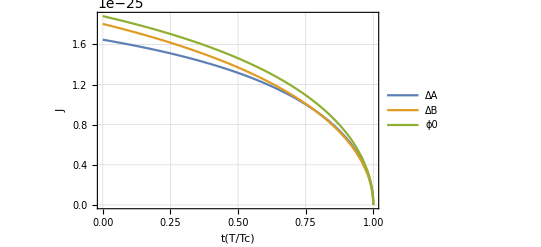

```mathematica
(*******************************************************************)
(**** take the SC GL model coefficients into the simplified f[ϕ] ***)
(*******************************************************************)
Clear[α,β,βwc1,βwc2,βwc3,βwc4,βwc5,βsc1,βsc2,βsc3,βsc4,βsc5,β1,β2,β3,β4,β5,βA,βB,gH,h,κ,θ,ϕ,ϕ0,k,c, J,eV,u,m,m3,ms,s,hz,Gauss,γ,F0a,vf,kf,Nf,t,T,Tc,kb,c1,c2,c3,c4,c5,c245,Δ2,ΔA,ΔB];
m=1;s=1;J=1;kg=1;k=1;Gauss=1;hz=1/s;
c=2.99792458 10^8 m s^-1;
hbar=1.054571817 10^-34 J s ;(* plank constant *)
kb=1.380649 10^-23 J k^-1;(**J.K^-1*)
(*π=3.1415926;*)
u= 1.66053906660 10^-27 kg ;
m3=3.016293 u;
(**pressure is 32 bar**)
ms=5.66 m3;
Tc=2.463 10^-3 k^-1;(*mK, kevin*)
vf=32.85 m s^-1;
kf=(vf ms)/hbar
Nf=(ms kf)/(2 π^2 hbar^2)
γ=-3243.409942 hz Gauss^-1
F0a=−0.7775

c1=-0.0402;c2 = -0.1583;c3=-0.0267;c4=-0.3388;c5=-0.3717;
(*******  All βi ********)
βwc1=-(7 Nf Zeta[3])/(240 π^2 kb^2 Tc^2);
βwc2=-2 βwc1;βwc3=-2 βwc1;βwc4=-2 βwc1;βwc5=2 βwc1;
βsc1=c1 Abs[βwc1];βsc2=c2 Abs[βwc1];
βsc3=c3 Abs[βwc1];
βsc4=c4 Abs[βwc1];
βsc5=c5 Abs[βwc1];
β1=βwc1+t βsc1;β2=βwc2+t βsc2;
β3=βwc3+t βsc3;
β4=βwc4+t βsc4;
β5=βwc5+t βsc5;
Print[Style["*******************",Red,18]]
gH=5 Abs[βwc1] ((γ hbar)/(1+F0a))^2
(***** Gap of A and B - phase *****)
Print[Style["*******************",Red,18]]
α=1/3 Nf (t-1);
βA=β2+β4+β5;
βB=β1+β2+1/3 (β3+β4+β5);
ΔA=√(-α/(2 βA))
ΔB=√(-α/(2 βB))
ϕ0=√(ΔA^2-√(2/3) ΔA ΔB+ΔB^2)
Plot[{ΔA,ΔB,ϕ0},{t,0,1},PlotLegends->"Expressions",AxesLabel->{Style["t(T/Tc)",15],Style["J",15]},Frame->True,GridLines->Automatic,PlotRangePadding->Scaled[.1]]
```

ϕ0 with t = 0.1, 0.3, 0.5, 0.7, 0.9 are: (unit is Juel)

{1.81636×10^-25,1.66175×10^-25,1.46211×10^-25,1.18428×10^-25,7.19069×10^-26}

-Graphics-

Plots of f[ϕ] with t > 0.8 :

-Graphics-

Plots of f[ϕ] with t > 0.8 :

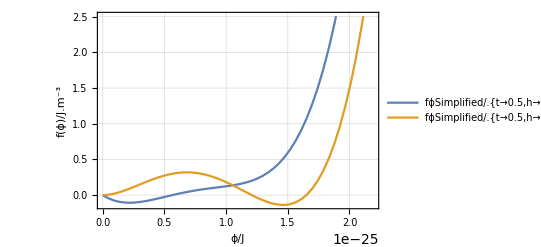

How f(ϕ0) Changes with t :

-Graphics-

```mathematica
(********* Plot the f(ϕ) at presure 32 bar **********)
ϕ0=√(ΔA^2-√(2/3) ΔA ΔB+ΔB^2);
(*h=0 Gauss;κ=π/6;*)
fϕSimplified=fϕ1Term+fϕ2Term+fϕ3Term+fϕ4Term;
Print[Style["ϕ0 with t = 0.1, 0.3, 0.5, 0.7, 0.9 are: (unit is Juel)",16,Red]]
{ϕ0/.t->0.1,ϕ0/.t->0.3,ϕ0/.t->0.5,ϕ0/.t->0.7,ϕ0/.t->0.9}
(*fϕ/.{ϕ->(ϕ0/.t->0.5),t->0.5}*)
(*******************************************************)
Plot[{fϕSimplified/.{t->0.0},fϕSimplified/.{t->0.1},fϕSimplified/.{t->0.3},fϕSimplified/.{t->0.5},fϕSimplified/.{t->0.7},fϕSimplified/.{t->0.9}},{ϕ,0,1.5(ϕ0/.t->0.5)},AxesLabel->{Style["ϕ/J",15],Style["f(ϕ)/J.m^-3",15]},Frame->True,GridLines->Automatic,PlotLegends->"Expressions",PlotRangePadding->{Scaled[.1],Scaled[.05]}]
(*******************************************************)
Print[Style[" Plots of f[ϕ] with t > 0.8 : " ,Red,16]]
Plot[{fϕSimplified/.{t->0.8},fϕSimplified/.{t->0.85},fϕSimplified/.{t->0.9},fϕSimplified/.{t->0.95},fϕSimplified/.{t->0.98}},{ϕ,0,1.5(ϕ0/.t->0.9)},AxesLabel->{Style["ϕ/J",15],Style["f(ϕ)/J.m^-3",15]},Frame->True,GridLines->Automatic,PlotLegends->"Expressions",PlotRangePadding->{Scaled[.1],Scaled[.15]}]
(*******************************************************)
Print[Style[" Plots of f[ϕ] with t > 0.8 : " ,Red,16]]
Plot[{fϕSimplified/.{t->0.5,h->90000 Gauss,κ->π/3},fϕSimplified/.{t->0.5,h->0 Gauss,κ->π/3}},{ϕ,0,1.5(ϕ0/.t->0.5)},AxesLabel->{Style["ϕ/J",15],Style["f(ϕ)/J.m^-3",15]},Frame->True,GridLines->Automatic,PlotLegends->"Expressions",PlotRangePadding->{Scaled[.1],Scaled[.15]}]
(******************************************************)
Print[Style[" How f(ϕ0) Changes with t :",16,Red]]
Plot[fϕSimplified/.{ϕ->ϕ0},{t,0.6,1.0},AxesLabel->{Style["t",15],Style["f(ϕ0)",15]},PlotLegends->"Expressions",Frame->True,GridLines->Automatic,PlotRangePadding->{Scaled[.1],Scaled[.07]}]
```